```mathematica
ClearAll["Global`*"]
```

```mathematica
(*This is CHATGPT's answer to the question 
Write a mathematica code to interpolate discrete point with a continuous curve
*)
```

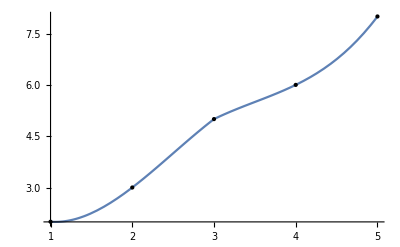

```mathematica
(*Define the data points*)data={{1,2},{2,3},{3,5},{4,6},{5,8}};

(*Perform polynomial interpolation*)
interp=Interpolation[data];

(*Plot the interpolated curve*)
Plot[interp[x],{x,1,5},Epilog->{PointSize[Medium],Point[data]}]
```